```mathematica
(* 1) run Read data, Construct form functions, Reconstruct solution*)
```

### Read data

```mathematica
SetDirectory[NotebookDirectory[]];SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop-Отладка"}]]
(*SetDirectory[FileNameJoin[{ParentDirectory[],"/build-RKDG2D-Desktop_Qt_5_10_1_MinGW_32bit-Debug"}]]*)
```

/home/darksy/build-RKDG2D-Desktop-Отладка

```mathematica
coeffs =Import["alphaCoeffs/0.200000","Table"];
mesh=Import["mesh2D","Table"];
```

```mathematica
Lx=mesh[[1,3]];
Ly=mesh[[2,3]];
nx=mesh[[3,3]];
ny=mesh[[4,3]];
hx=mesh[[5,3]];
hy=mesh[[6,3]];
numFF=mesh[[7,3]];
MeshCellArea=hx*hy;
MeshCellRcm=mesh[[9;;]];
nCells=Length@MeshCellRcm;
alpha=Table[Partition[coeffs[[i]],numFF],{i,1,nCells}];
```

#### Construct form functions

```mathematica
Phi0[n_,r_]:=1./(√MeshCellArea)
Phi10[n_,r_List]:=√(12./(hy hx^3))(r[[1]]-MeshCellRcm[[n,1]])
Phi11[n_,r_List]:=√(12./(hy^3 hx))(r[[2]]-MeshCellRcm[[n,2]])
Phi20[n_,r_List]:=√(180./(hy hx^5))((r[[1]]-MeshCellRcm[[n,1]])^2-hx^2/12)
Phi21[n_,r_List]:=√(144./(hy^3 hx^3))(r[[1]]-MeshCellRcm[[n,1]])(r[[2]]-MeshCellRcm[[n,2]])
Phi22[n_,r_List]:=√(180./(hy^5 hx))((r[[2]]-MeshCellRcm[[n,2]])^2-hy^2/12)

Phi[n_,r_List]:={Phi0[n,r],Phi10[n,r],Phi11[n,r],Phi20[n,r],Phi21[n,r],Phi22[n,r]}
```

#### Reconstruct solution

```mathematica
GetSol[alpha_,n_,numSol_,r_List]:=Sum[Phi[n,r][[i]]alpha[[n,numSol,i]],{i,numFF}];
```

```mathematica
GetSolDensity[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
GetSolGraphics[alpha_,n_,numSol_]:=Module[{pts,anSol},(
pts={{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]-hy/2.0},
{MeshCellRcm[[n,1]]+hx/2.0,MeshCellRcm[[n,2]]+hy/2.0},
{MeshCellRcm[[n,1]]-hx/2.0,MeshCellRcm[[n,2]]+hy/2.0}};
anSol=Table[GetSol[alpha,n,numSol,pts[[i]]],{i,1,4}];
Return[Polygon@Table[{pts[[i,1]],pts[[i,2]],anSol[[i]]},{i,1,4}]]
)];
```

#### Compute integral

```mathematica
(MeshCellRcm[[i]]/.{i->10})-{Lx/2,Ly/2}
GetSol[alpha,i,1,MeshCellRcm[[i]]]/.i->200
```

Part::pkspec1: The expression i cannot be used as a part specification.

{-0.405,0.}

Part::pkspec1: The expression i cannot be used as a part specification.

Part::partw: Part 200 of {{0.005,0.5},{0.015,0.5},{0.025,0.5},{0.035,0.5},{0.045,0.5},{0.055,0.5},{0.065,0.5},{0.075,0.5},{0.085,0.5},{0.095,0.5},{0.105,0.5},«29»,{0.405,0.5},{0.415,0.5},{0.425,0.5},{0.435,0.5},{0.445,0.5},{0.455,0.5},{0.465,0.5},{0.475,0.5},{0.485,0.5},{0.495,0.5},«50»} does not exist.

GetSol[{{{0.1,1.45996×10^-14,0},{-2.05627×10^-13,-1.68505×10^-14,0},{0,0,3.60822×10^-19},{0,0,0},{0.25,5.12094×10^-14,0}},{{0.1,-3.32086×10^-13,0},{7.43491×10^-13,3.93387×10^-13,0},{0,0,4.35706×10^-19},{0,0,0},{0.25,-1.16234×10^-12,0}},{{0.1,1.27712×10^-12,0},{-1.49211×10^-12,-1.51069×10^-12,0},{0,0,3.95416×10^-19},{0,0,0},{0.25,4.46993×10^-12,0}},{{0.1,-2.40745×10^-12,0},{-3.84578×10^-13,2.84892×10^-12,0},{0,0,3.38729×10^-19},{0,0,0},{0.25,-8.42607×10^-12,0}},{{0.1,-1.16231×10^-12,0},{1.42358×10^-11,1.37568×10^-12,0},{0,0,3.36038×10^-19},{0,0,0},{0.25,-4.0682×10^-12,0}},{{0.1,2.44051×10^-11,0},{-5.19221×10^-11,-2.88762×10^-11,0},{0,0,2.75751×10^-19},{0,0,0},{0.25,8.54181×10^-11,0}},{{0.1,-8.09762×10^-11,0},{7.50447×10^-11,9.58126×10^-11,0},{0,0,2.40331×10^-19},{0,0,0},{0.25,-2.83416×10^-10,0}},{{0.1,9.40331×10^-11,0},{1.54873×10^-10,-1.11261×10^-10,0},{0,0,2.47922×10^-19},{0,0,0},{0.25,3.29116×10^-10,0}},{{0.1,3.06684×10^-10,0},{-1.12663×10^-9,-3.62873×10^-10,0},{0,0,3.04369×10^-19},{0,0,0},{0.25,1.07339×10^-9,0}},{{0.1,-1.69018×10^-9,0},{2.45992×10^-9,1.99985×10^-9,0},{0,0,3.51103×10^-19},{0,0,0},{0.25,-5.91562×10^-9,0}},{{0.1,2.91237×10^-9,0},{8.567×10^-10,-3.44596×10^-9,0},{0,0,2.18878×10^-19},{0,0,0},{0.25,1.01933×10^-8,0}},{{0.1,3.36412×10^-9,0},{-1.97705×10^-8,-3.98045×10^-9,0},{0,0,2.37909×10^-19},{0,0,0},{0.25,1.17743×10^-8,0}},{{0.1,-2.72695×10^-8,0},{4.45704×10^-8,3.22655×10^-8,0},{0,0,1.33258×10^-19},{0,0,0},{0.25,-9.54426×10^-8,0}},{{0.1,4.07439×10^-8,0},{2.61551×10^-8,-4.82065×10^-8,0},{0,0,1.58045×10^-19},{0,0,0},{0.25,1.42597×10^-7,0}},{{0.1,7.97085×10^-8,0},{-3.28149×10^-7,-9.43281×10^-8,0},{0,0,1.72739×10^-19},{0,0,0},{0.250001,2.79026×10^-7,0}},{{0.0999997,-3.62308×10^-7,0},{4.01762×10^-7,4.28764×10^-7,0},{0,0,1.65173×10^-19},{0,0,0},{0.249999,-1.2683×10^-6,0}},{{0.0999989,6.50365×10^-8,0},{1.33651×10^-6,-7.71886×10^-8,0},{0,0,2.10398×10^-19},{0,0,0},{0.249996,2.28326×10^-7,0}},{{0.100003,1.84165×10^-6,0},{-3.76939×10^-6,-2.17956×10^-6,0},{0,0,1.36465×10^-19},{0,0,0},{0.250011,6.44712×10^-6,0}},{{0.100004,-1.80134×10^-6,0},{-4.14456×10^-6,2.14268×10^-6,0},{0,0,1.53438×10^-19},{0,0,0},{0.250012,-6.33814×10^-6,0}},{{0.0999813,-8.25792×10^-6,0},{0.0000221021,9.81281×10^-6,0},{0,0,1.51361×10^-19},{0,0,0},{0.249935,-0.0000288672,0}},{{0.0999808,7.98842×10^-6,0},{0.0000225164,-9.76354×10^-6,0},{0,0,1.27945×10^-19},{0,0,0},{0.249933,0.0000287835,0}},{{0.100098,0.0000479857,0},{-0.000117381,-0.0000606315,0},{0,0,1.16879×10^-19},{0,0,0},{0.250347,0.000179403,0}},{{0.10029,0.0000523205,0},{-0.000353214,-0.0000718865,0},{0,0,7.60348×10^-20},{0,0,0},{0.251068,0.0000505102,0}},{{0.100406,0.0000133457,0},{-0.000485401,9.86302×10^-6,0},{0,0,4.49142×10^-20},{0,0,0},{0.251451,9.97898×10^-6,0}},{{0.0999035,-0.000247557,0},{0.000122599,0.000277833,0},{0,0,2.0011×10^-20},{0,0,0},{0.249641,-0.00085048,0}},{{0.0984726,-0.000489367,0},{0.00178027,0.000573996,0},{0,0,5.82696×10^-20},{0,0,0},{0.244697,-0.00168836,0}},{{0.0963609,-0.000664166,0},{0.0042054,0.000745375,0},{0,0,4.69675×10^-20},{0,0,0},{0.237473,-0.00225792,0}},{{0.0938498,-0.000752089,0},{0.00699011,0.000824077,0},{0,0,-1.13516×10^-20},{0,0,0},{0.229027,-0.00250409,0}},{{0.0911608,-0.000791853,0},{0.00989088,0.000835301,0},{0,0,-2.79834×10^-20},{0,0,0},{0.22016,-0.00258707,0}},{{0.0883878,-0.000811454,0},{0.0127527,0.000815795,0},{0,0,8.5204×10^-20},{0,0,0},{0.211234,-0.00257131,0}},{{0.0855885,-0.000813326,0},{0.0155133,0.000780476,0},{0,0,9.93609×10^-20},{0,0,0},{0.202474,-0.00251128,0}},{{0.0828019,-0.000805723,0},{0.018134,0.000737611,0},{0,0,1.52666×10^-19},{0,0,0},{0.193967,-0.00242975,0}},{{0.0800514,-0.000793872,0},{0.0206017,0.000691633,0},{0,0,8.79101×10^-20},{0,0,0},{0.185768,-0.002336,0}},{{0.0773442,-0.000780854,0},{0.0229058,0.000642971,0},{0,0,3.2178×10^-20},{0,0,0},{0.177897,-0.00223937,0}},{{0.0746867,-0.000765116,0},{0.0250437,0.000594817,0},{0,0,-4.4507×10^-20},{0,0,0},{0.170366,-0.00213884,0}},{{0.0720863,-0.00074746,0},{0.0270162,0.000546634,0},{0,0,1.60602×10^-20},{0,0,0},{0.163176,-0.00204055,0}},{{0.069546,-0.000729919,0},{0.0288251,0.000499712,0},{0,0,1.09748×10^-19},{0,0,0},{0.156322,-0.00194157,0}},{{0.0670642,-0.000713828,0},{0.0304735,0.000452466,0},{0,0,1.36692×10^-19},{0,0,0},{0.149804,-0.00184649,0}},{{0.0646388,-0.000696462,0},{0.0319612,0.000406439,0},{0,0,1.32592×10^-19},{0,0,0},{0.143604,-0.0017548,0}},{{0.0622755,-0.000677381,0},{0.0332952,0.000362994,0},{0,0,1.14648×10^-19},{0,0,0},{0.137717,-0.00166438,0}},{{0.0599778,-0.00065816,0},{0.0344822,0.00032064,0},{0,0,1.10898×10^-19},{0,0,0},{0.132132,-0.00157839,0}},{{0.0577471,-0.00063793,0},{0.0355267,0.000280386,0},{0,0,1.11356×10^-19},{0,0,0},{0.126838,-0.00149513,0}},{{0.0555867,-0.000617137,0},{0.0364363,0.000242124,0},{0,0,1.15854×10^-19},{0,0,0},{0.121825,-0.00141394,0}},{{0.0534972,-0.000596727,0},{0.0372159,0.000204678,0},{0,0,9.22358×10^-20},{0,0,0},{0.117087,-0.00133538,0}},{{0.0514796,-0.000575063,0},{0.037869,0.00016879,0},{0,0,7.11216×10^-20},{0,0,0},{0.112619,-0.00125736,0}},{{0.0495425,-0.000549584,0},{0.0384025,0.000135529,0},{0,0,4.78352×10^-20},{0,0,0},{0.108422,-0.00117711,0}},{{0.0477028,-0.000518271,0},{0.038825,0.000104745,0},{0,0,3.6289×10^-20},{0,0,0},{0.104513,-0.00108992,0}},{{0.0459881,-0.00047691,0},{0.0391438,0.0000757284,0},{0,0,-3.08083×10^-20},{0,0,0},{0.100934,-0.000985608,0}},{{0.0444536,-0.000413995,0},{0.039364,0.0000481055,0},{0,0,-3.59982×10^-20},{0,0,0},{0.097785,-0.000840674,0}},{{0.0432264,-0.000298195,0},{0.0394928,0.0000246408,0},{0,0,-4.0303×10^-20},{0,0,0},{0.0953052,-0.000597695,0}},{{0.0425632,-0.0000887023,0},{0.0395436,3.79572×10^-6,0},{0,0,-3.81723×10^-20},{0,0,0},{0.0939799,-0.000173948,0}},{{0.0424813,0.0000404802,0},{0.0395446,-2.53217×10^-6,0},{0,0,-3.37376×10^-20},{0,0,0},{0.0938253,0.000077111,0}},{{0.0425625,6.54543×10^-6,0},{0.0395383,-9.79589×10^-7,0},{0,0,-3.71662×10^-20},{0,0,0},{0.0939817,0.0000135453,0}},{{0.0425743,4.97706×10^-7,0},{0.0395362,-1.05743×10^-7,0},{0,0,-2.68003×10^-20},{0,0,0},{0.0940071,1.58519×10^-6,0}},{{0.0425991,0.0000137456,0},{0.0395352,-4.41979×10^-7,0},{0,0,-9.93781×10^-21},{0,0,0},{0.0940578,0.0000274741,0}},{{0.0426711,0.0000277078,0},{0.0395339,-1.61848×10^-7,0},{0,0,5.9191×10^-21},{0,0,0},{0.094199,0.0000526121,0}},{{0.0427342,8.9383×10^-6,0},{0.039536,1.44206×10^-6,0},{0,0,2.70388×10^-20},{0,0,0},{0.094315,0.0000145732,0}},{{0.0427188,-0.0000177763,0},{0.0395416,1.39297×10^-6,0},{0,0,2.37983×10^-20},{0,0,0},{0.094277,-0.0000356697,0}},{{0.0426481,-0.0000248275,0},{0.0395377,-5.11599×10^-6,0},{0,0,3.46881×10^-20},{0,0,0},{0.0941503,-0.0000384077,0}},{{0.0425628,-0.0000240032,0},{0.0395186,-5.6577×10^-6,0},{0,0,4.44978×10^-20},{0,0,0},{0.0940209,-0.0000360424,0}},{{0.0425412,0.0000163958,0},{0.0395227,0.0000128232,0},{0,0,3.34222×10^-20},{0,0,0},{0.0939748,0.0000108775,0}},{{0.0426168,0.0000282225,0},{0.0395845,0.0000237981,0},{0,0,3.32991×10^-20},{0,0,0},{0.0940204,0.0000159528,0}},{{0.0426475,-0.0000201422,0},{0.0396212,-0.0000117472,0},{0,0,3.50983×10^-20},{0,0,0},{0.0940213,-0.0000191496,0}},{{0.0425404,-0.0000466966,0},{0.039526,-0.0000478405,0},{0,0,3.58129×10^-20},{0,0,0},{0.0939704,-0.0000133377,0}},{{0.0424333,-6.03228×10^-7,0},{0.039395,-0.0000139738,0},{0,0,3.0551×10^-20},{0,0,0},{0.0939723,0.0000199403,0}},{{0.0423407,-0.0000646454,0},{0.0392867,-0.0000599826,0},{0,0,2.25963×10^-20},{0,0,0},{0.0939651,-0.0000278716,0}},{{0.0414974,-0.00052907,0},{0.038467,-0.000511308,0},{0,0,3.80976×10^-20},{0,0,0},{0.093664,-0.000192764,0}},{{0.0385744,-0.00127894,0},{0.0357656,-0.00116201,0},{0,0,4.11016×10^-20},{0,0,0},{0.0923933,-0.000592691,0}},{{0.0338162,-0.00147333,0},{0.0313928,-0.00136684,0},{0,0,4.28326×10^-20},{0,0,0},{0.0902691,-0.000636881,0}},{{0.029404,-0.000975192,0},{0.02726,-0.000925043,0},{0,0,3.13152×10^-20},{0,0,0},{0.0884473,-0.000374164,0}},{{0.0269244,-0.000364273,0},{0.024941,-0.000330837,0},{0,0,3.35698×10^-20},{0,0,0},{0.0874256,-0.000171552,0}},{{0.0261451,-0.0000569765,0},{0.0242511,-0.0000413938,0},{0,0,2.92455×10^-20},{0,0,0},{0.0870165,-0.0000516163,0}},{{0.0260495,-9.02362×10^-7,0},{0.0241747,-3.82368×10^-6,0},{0,0,3.53311×10^-20},{0,0,0},{0.086943,5.27813×10^-6,0}},{{0.0260464,5.17991×10^-8,0},{0.0241599,-3.98984×10^-6,0},{0,0,4.34459×10^-20},{0,0,0},{0.0869668,9.56166×10^-6,0}},{{0.0260797,0.0000233564,0},{0.0241781,0.0000184191,0},{0,0,3.41238×10^-20},{0,0,0},{0.0870123,0.0000180282,0}},{{0.0261912,0.000044285,0},{0.0242751,0.0000399295,0},{0,0,2.78459×10^-20},{0,0,0},{0.0870744,0.0000195807,0}},{{0.0263924,0.0000722714,0},{0.0244141,0.0000416095,0},{0,0,3.47897×10^-20},{0,0,0},{0.0872564,0.0000829567,0}},{{0.0266323,0.0000594048,0},{0.0245241,0.0000186386,0},{0,0,4.65649×10^-20},{0,0,0},{0.0875931,0.000103245,0}},{{0.0266906,-0.0000290863,0},{0.02457,-8.83391×10^-7,0},{0,0,3.93571×10^-20},{0,0,0},{0.0876305,-0.0000704869,0}},{{0.0266185,-2.18464×10^-6,0},{0.0246091,0.000034237,0},{0,0,3.25×10^-20},{0,0,0},{0.0873613,-0.0000835913,0}},{{0.0266738,0.0000398905,0},{0.0248013,0.0000748399,0},{0,0,3.67796×10^-20},{0,0,0},{0.0870764,-0.0000785498,0}},{{0.0267391,-0.0000181888,0},{0.024981,4.52255×10^-6,0},{0,0,4.33773×10^-20},{0,0,0},{0.0868443,-0.0000541544,0}},{{0.0265208,-0.000155998,0},{0.0248009,-0.000219794,0},{0,0,3.95789×10^-20},{0,0,0},{0.0866532,-0.000153582,0}},{{0.0259979,-0.000292249,0},{0.0239377,-0.000603512,0},{0,0,4.44667×10^-20},{0,0,0},{0.0855032,-0.00142163,0}},{{0.0240242,-0.001009,0},{0.0194766,-0.00210104,0},{0,0,5.10165×10^-20},{0,0,0},{0.0747721,-0.00475109,0}},{{0.017479,-0.00193129,0},{0.00721806,-0.00266122,0},{0,0,4.03802×10^-20},{0,0,0},{0.0434911,-0.0067102,0}},{{0.0127962,-0.000576907,0},{0.000374356,-0.000771648,0},{0,0,1.17767×10^-20},{0,0,0},{0.0259784,-0.00194546,0}},{{0.0122899,0.0000835667,0},{-0.000220281,0.000107293,0},{0,0,-5.92924×10^-22},{0,0,0},{0.0243674,0.000134697,0}},{{0.012498,9.91501×10^-6,0},{-8.30794×10^-6,0.0000204161,0},{0,0,-1.05221×10^-20},{0,0,0},{0.0249781,0.000053909,0}},{{0.0125025,-3.13325×10^-6,0},{2.84572×10^-6,-3.84606×10^-6,0},{0,0,-6.29488×10^-21},{0,0,0},{0.0250075,-0.0000101963,0}},{{0.0124993,8.83026×10^-7,0},{-6.59796×10^-7,8.65627×10^-7,0},{0,0,-4.92782×10^-21},{0,0,0},{0.0249983,2.29037×10^-6,0}},{{0.0125001,-1.74198×10^-7,0},{8.43458×10^-8,-1.56575×10^-7,0},{0,0,-5.73355×10^-21},{0,0,0},{0.0250002,-4.1425×10^-7,0}},{{0.0125,2.51318×10^-8,0},{5.42324×10^-9,2.13165×10^-8,0},{0,0,2.59489×10^-21},{0,0,0},{0.025,5.63986×10^-8,0}},{{0.0125,-1.36651×10^-9,0},{-8.04043×10^-9,-7.07653×10^-10,0},{0,0,-3.35806×10^-21},{0,0,0},{0.025,-1.87225×10^-9,0}},{{0.0125,-8.16125×10^-10,0},{3.46719×10^-9,-9.46982×10^-10,0},{0,0,9.15347×10^-21},{0,0,0},{0.025,-2.50548×10^-9,0}},{{0.0125,4.53277×10^-10,0},{-1.14201×10^-9,4.87421×10^-10,0},{0,0,1.43262×10^-20},{0,0,0},{0.025,1.2896×10^-9,0}},{{0.0125,-1.5957×10^-10,0},{3.27498×10^-10,-1.6945×10^-10,0},{0,0,-1.90529×10^-21},{0,0,0},{0.025,-4.48324×10^-10,0}},{{0.0125,4.64145×10^-11,0},{-8.58122×10^-11,4.9153×10^-11,0},{0,0,2.71897×10^-21},{0,0,0},{0.025,1.30047×10^-10,0}},{{0.0125,-1.19614×10^-11,0},{2.11108×10^-11,-1.26599×10^-11,0},{0,0,6.00184×10^-21},{0,0,0},{0.025,-3.34948×10^-11,0}},{{0.0125,2.82339×10^-12,0},{-4.97903×10^-12,2.98798×10^-12,0},{0,0,1.21977×10^-21},{0,0,0},{0.025,7.90542×10^-12,0}}},200,1,{{0.005,0.5},{0.015,0.5},{0.025,0.5},{0.035,0.5},{0.045,0.5},{0.055,0.5},{0.065,0.5},{0.075,0.5},{0.085,0.5},{0.095,0.5},{0.105,0.5},{0.115,0.5},{0.125,0.5},{0.135,0.5},{0.145,0.5},{0.155,0.5},{0.165,0.5},{0.175,0.5},{0.185,0.5},{0.195,0.5},{0.205,0.5},{0.215,0.5},{0.225,0.5},{0.235,0.5},{0.245,0.5},{0.255,0.5},{0.265,0.5},{0.275,0.5},{0.285,0.5},{0.295,0.5},{0.305,0.5},{0.315,0.5},{0.325,0.5},{0.335,0.5},{0.345,0.5},{0.355,0.5},{0.365,0.5},{0.375,0.5},{0.385,0.5},{0.395,0.5},{0.405,0.5},{0.415,0.5},{0.425,0.5},{0.435,0.5},{0.445,0.5},{0.455,0.5},{0.465,0.5},{0.475,0.5},{0.485,0.5},{0.495,0.5},{0.505,0.5},{0.515,0.5},{0.525,0.5},{0.535,0.5},{0.545,0.5},{0.555,0.5},{0.565,0.5},{0.575,0.5},{0.585,0.5},{0.595,0.5},{0.605,0.5},{0.615,0.5},{0.625,0.5},{0.635,0.5},{0.645,0.5},{0.655,0.5},{0.665,0.5},{0.675,0.5},{0.685,0.5},{0.695,0.5},{0.705,0.5},{0.715,0.5},{0.725,0.5},{0.735,0.5},{0.745,0.5},{0.755,0.5},{0.765,0.5},{0.775,0.5},{0.785,0.5},{0.795,0.5},{0.805,0.5},{0.815,0.5},{0.825,0.5},{0.835,0.5},{0.845,0.5},{0.855,0.5},{0.865,0.5},{0.875,0.5},{0.885,0.5},{0.895,0.5},{0.905,0.5},{0.915,0.5},{0.925,0.5},{0.935,0.5},{0.945,0.5},{0.955,0.5},{0.965,0.5},{0.975,0.5},{0.985,0.5},{0.995,0.5}}⟦200⟧]

```mathematica
hx hy Sum[GetSol[alpha,i,1,MeshCellRcm[[i]]],{i,1,nCells}]
```

0.5625

```mathematica
16.0004592
```

16.0005

```mathematica
16.000465920000014 -16.000460079999883
```

5.84×10^-6

```mathematica
16.000460079999883
```

16.0005

```mathematica
16.0004592 -16.000460079999883
```

-8.8×10^-7

```mathematica
16.00156879999998
```

16.0016

#### Draw solution Graphics

```mathematica
Graphics3D[Table[GetSolGraphics[alpha,i,1],{i,1,nCells}]]
```

-Graphics3D-

#### Draw in diag

```mathematica
diagPoints=Table[MeshCellRcm[[i]]-0.5{hx,hy},{i,1,nCells,nx+1}]~Join~{MeshCellRcm[[nCells]]+0.5{hx,hy}};
diagV=diagPoints[[2]]-diagPoints[[1]];
diagH=Norm[diagV,2];
diagX=Table[i*diagH,{i,0,Length[diagPoints]-1}];
diagVal=Table[{GetSol[alpha,i,1,MeshCellRcm[[i]]-0.5{hx,hy}],GetSol[alpha,i,1,MeshCellRcm[[i]]+0.5{hx,hy}]},{i,1,nCells,nx+1}];
```

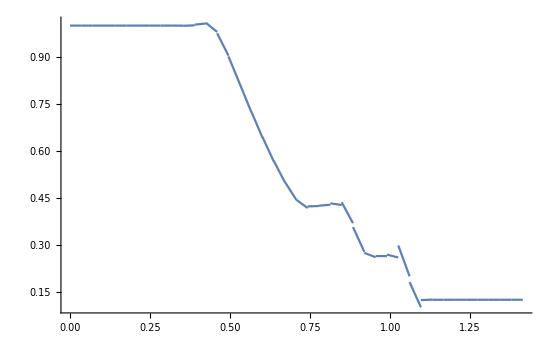

```mathematica
ggg=Show[Table[ListLinePlot[{{diagX[[i]],diagVal[[i,1]]},{diagX[[i+1]],diagVal[[i,2]]}}],{i,1,Length[diagX]-1}],PlotRange->All]
```

Draw in diag cell average

```mathematica
Norm[MeshCellRcm[[1]],2]
```

0.0176777

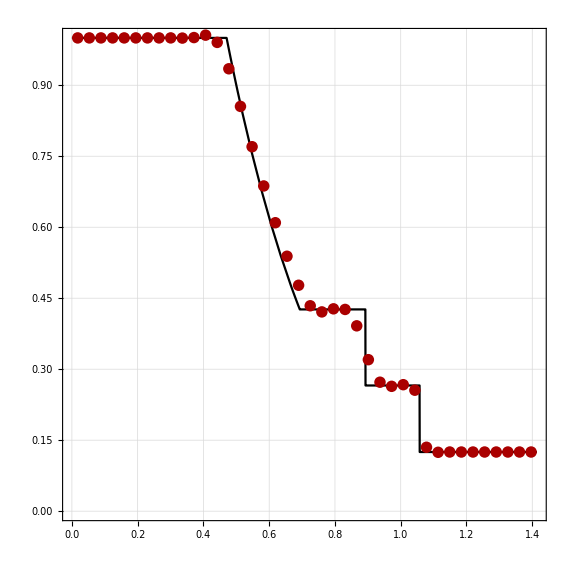

```mathematica
mcc=Table[MeshCellRcm[[i]],{i,1,nCells,nx+1}];
mcy=Table[GetSol[alpha,i,1,MeshCellRcm[[i]]],{i,1,nCells,nx+1}];
mcx=Table[Norm[mcc[[i]],2],{i,Length[mcc]}];
exactDiag=Plot[ρ[x-(√2-1)/2,0.2],{x,0,√2},PlotStyle->Black,Exclusions->None];
grsode=Show[exactDiag,ListPlot[Transpose@{mcx,mcy},
PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
Export["LLF+WENOS.png",grsode,ImageResolution->300]
```

LLF+WENOS.png

#### Draw in X or Y direction

```mathematica
bou=MeshCellRcm[[All,1]]-hx/2;
```

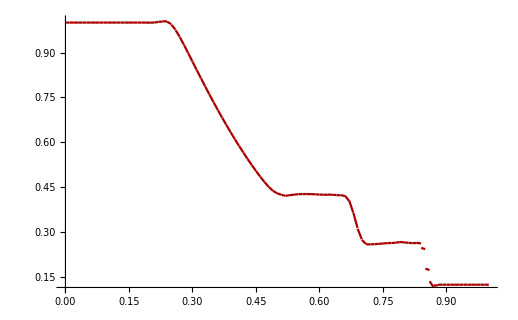

```mathematica
funVis1D[y_]:=Piecewise[Table[{GetSol[alpha,i,1,{0,y}],MeshCellRcm[[i,2]]-hy/2.0 < y <MeshCellRcm[[i,2]]+hy/2.0},{i,1,nCells}]];
funVis1D[x_]:=Piecewise[Table[{(GetSol[alpha,i,1,{x,hy/2}]/1),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,1,nx}]];
fig2e=Plot[funVis1D[x],{x,0,Lx},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]]
```

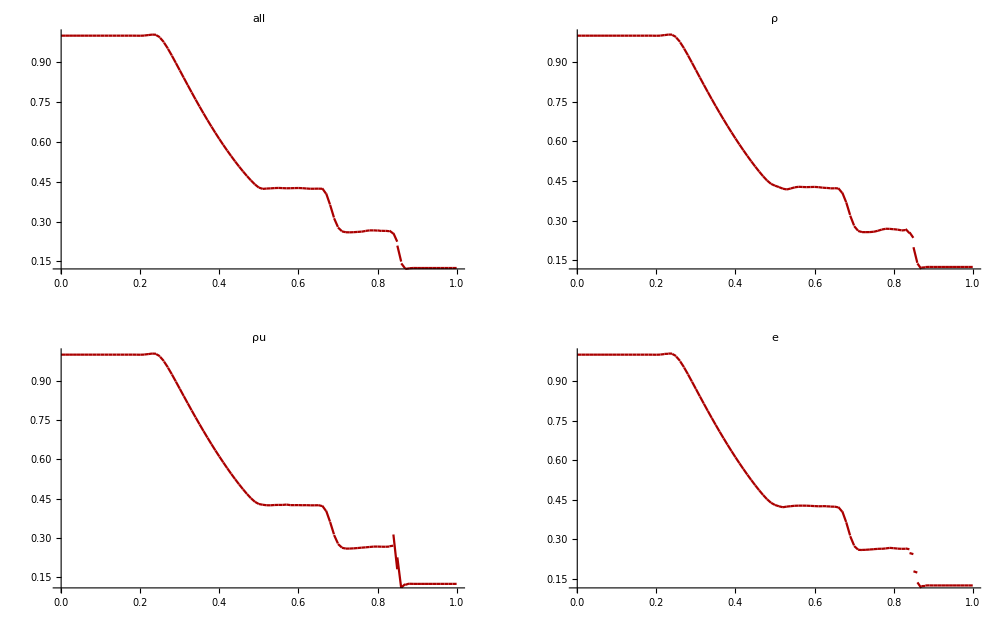

```mathematica
full=GraphicsGrid[{{Show[fig2all,PlotLabel->"all",LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[fig2rho,PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black]},
{Show[fig2rhou,PlotLabel->"ρu",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[fig2e,PlotLabel->"e",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]}},
Frame->All,ImageSize->1000]
```

```mathematica
Export["full.jpg",full]
```

full.jpg

```mathematica
Integrate[√(R^2-x^2),{x,0,R}]
```

1/4 π R √(R^2)

```mathematica
getPressure[x_,i_]:=(1.4-1)(GetSol[alpha,i,5,{x,(Lx+hx)/2}]-1/2((GetSol[alpha,i,2,{x,(Lx+hx)/2}]^2+GetSol[alpha,i,3,{x,(Lx+hx)/2}]^2+GetSol[alpha,i,4,{x,(Lx+hx)/2}]^2)/GetSol[alpha,i,1,{x,(Lx+hx)/2}]))
```

```mathematica
getEnthalpy[x_,i_]:=(getPressure[x,i]+GetSol[alpha,i,5,{x,(Lx+hx)/2}])/GetSol[alpha,i,1,{x,(Lx+hx)/2}]
```

```mathematica
funVisp1D[x_]:=Piecewise[Table[{(getPressure[x,i]),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
grp=Plot[funVisp1D[x],{x,0,12},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]];
```

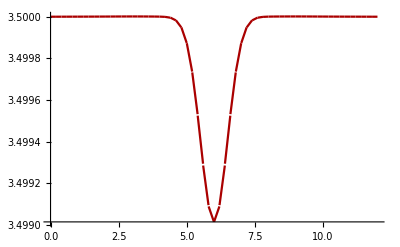

```mathematica
funVish1D[x_]:=Piecewise[Table[{(getEnthalpy[x,i]),MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,nx ny/2+1,nx ny/2+nx}]];
grh=Plot[funVish1D[x],{x,0,12},Exclusions->bou,PlotPoints->100,PlotRange->All,PlotStyle->Darker[Red]]
```

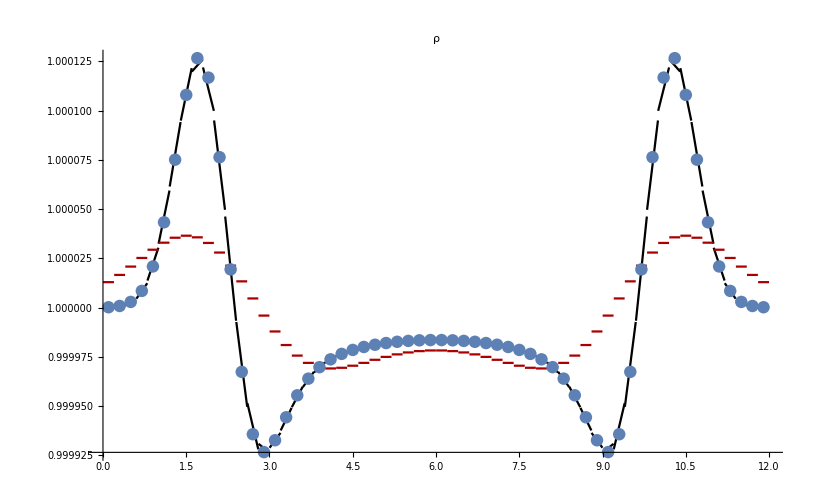

```mathematica
Show[fig1,fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black]
```

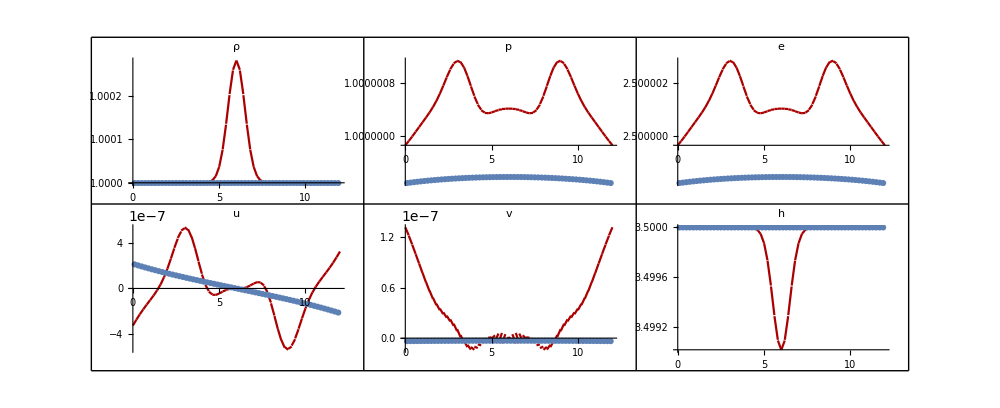

```mathematica
full=GraphicsGrid[{{Show[fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"ρ",LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[grp,ListPlot[dataAnCenterRhoEqP,PlotRange->All],PlotLabel->"p",LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[fig2e,ListPlot[dataAnCenterE,PlotRange->All],PlotLabel->"e",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]},
{Show[fig2U,ListPlot[dataAnCenterU,PlotRange->All],PlotLabel->"u",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],Show[fig2V,ListPlot[dataAnCenterV,PlotRange->All],PlotLabel->"v",
LabelStyle->Directive[{Black,12}],AxesStyle->Black],
Show[grh,ListPlot[dataAnCenterH,PlotRange->All],PlotLabel->"h",
LabelStyle->Directive[{Black,12}],AxesStyle->Black]}},
Frame->All,ImageSize->1000]
```

```mathematica
Export["t=20.jpg",full,ImageResolution->150]
```

t=20.jpg

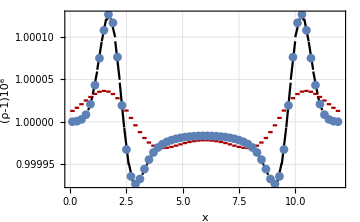

```mathematica
grd=Table[MeshCellRcm[[i,1]]-hx/2,{i,1,nx}]~Join~{MeshCellRcm[[nx,1]]+hx/2};
ee=Show[fig1,fig2,ListPlot[dataAnCenterRhoEqP,PlotRange->All,PlotMarkers->Automatic],
Frame->True,
GridLines->{grd,Automatic},
ImageSize->Medium,
LabelStyle->Directive[Black,12,FontFamily->"Times"],
FrameLabel->{"x","(ρ-1)10^6"}]
```

```mathematica
Export["LF_t=2.png",ee,ImageResolution->300]
```

LF_t=2.png

#### Draw Sode problem

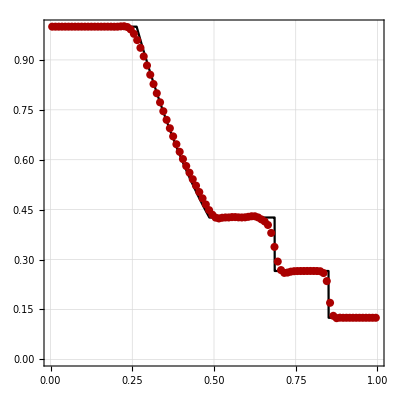

```mathematica
exact=Plot[ρ[x,0.2],{x,0,1},PlotStyle->Black,Exclusions->None];
grsode=Show[exact,ListPlot[Table[{MeshCellRcm[[i,1]],GetSol[alpha,i,1,MeshCellRcm[[i]]]},{i,1,nx}],PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
grsodeDiag=Show[exact,ListPlot[Table[{MeshCellRcm[[i,1]],GetSol[alpha,i,1,MeshCellRcm[[i]]]},{i,1,nx}],PlotStyle->{Darker[Red],PointSize[0.0145]}],AspectRatio->1,
Frame->True,
FrameStyle->Black,
GridLines->Automatic,
LabelStyle->Directive[12,FontFamily->"Times"]]
```

```mathematica
Export["HLLC+WENOS+Everywhere.png",grsode,ImageResolution->300]
```

HLLC+WENOS+Everywhere.png

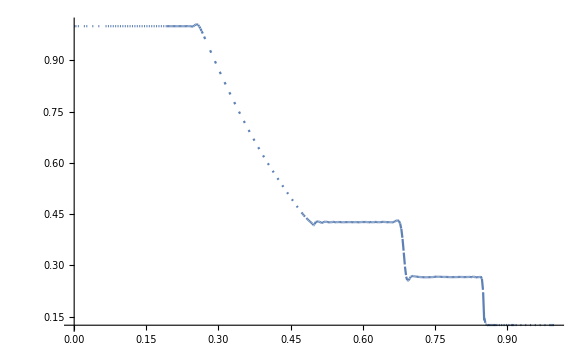

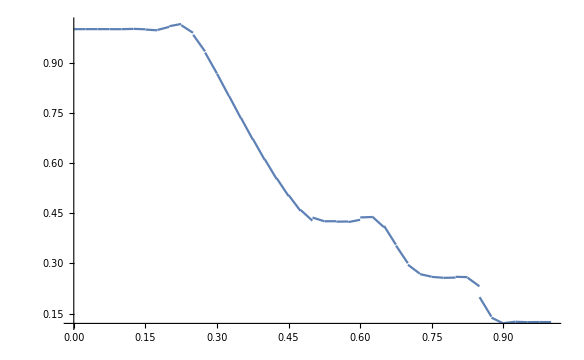

```mathematica
troubledCells={50,51}+1
funVis1DLim[x_]:=Piecewise[Table[{GetSol[alpha,i,1,{x,0}],MeshCellRcm[[i,1]]-hx/2.0 < x <MeshCellRcm[[i,1]]+hx/2.0},{i,troubledCells}]];
```

{51,52}

```mathematica
trb=Plot[funVis1DLim[x],{x,0,1},PlotStyle->Red,Exclusions->bou,PlotPoints->200];
```

Part::partw: Part 51 of {{0.0125,0.25},{0.0375,0.25},{0.0625,0.25},{0.0875,0.25},{0.1125,0.25},{0.1375,0.25},{0.1625,0.25},{0.1875,0.25},{0.2125,0.25},{0.2375,0.25},{0.2625,0.25},{0.2875,0.25},«16»,{0.7125,0.25},{0.7375,0.25},{0.7625,0.25},{0.7875,0.25},{0.8125,0.25},{0.8375,0.25},{0.8625,0.25},{0.8875,0.25},{0.9125,0.25},{0.9375,0.25},{0.9625,0.25},{0.9875,0.25}} does not exist.

Part::partw: Part 51 of {{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}},{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}},«37»,{{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan},{nan,nan,nan}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Show[fig,trb]
```

-Graphics-

#### Draw density plot

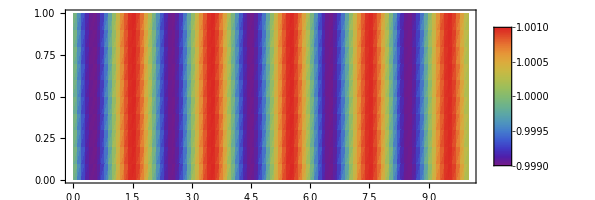

```mathematica
ListDensityPlot[Table[GetSolDensity[alpha,i,1],{i,1,nCells}],AspectRatio->Automatic,PlotRange->All,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```